ElectroDynamics, by James Rohlf and Kevin Reiss, Version 2.0, Copyright 2022, All Rights Reserved.

__________________________________________________________________________________

Section | Electrostatics

1.1 Constants and Units
	1.2 Notation
	1.3 Coulomb's Law
	1.4 Electric Field
	1.5 Electric Flux and Gauss's Law
	1.6 Divergence and Curl
	1.7 Electric Potential
	1.8 Electric Dipole
	1.9 Energy of a Charge Distribution
	1.10 Conductors
	1.11 Laplace's Equation
	1.12 Summary of E, V, and ρ

The electric dipole plays a fundamental role in electromagnetism, from statics to radiation, and the electric potential is an invaluable concept for its visualization and interpretation.

```mathematica
(Column[{#[EntityProperty["WolframDemonstration","WolframDemonstrationsLink"]]/.Hyperlink[link_]:>Hyperlink[#[EntityProperty["WolframDemonstration","Name"]],link],Row[{"By: "}~Join~Riffle[(Hyperlink[#["Name"],First[#["ContributorLink"]]])&/@#[EntityProperty["WolframDemonstration","Authors"]],", "]],#[EntityProperty["WolframDemonstration","Manipulate"]],}]&)[Entity["WolframDemonstration","ElectricDipolePotential"]]
```

[Electric Dipole Potential ](https://demonstrations.wolfram.com/ElectricDipolePotential)
By: [Stephen Wolfram](http://demonstrations.wolfram.com/author.html?author=Stephen+Wolfram)

```mathematica
pot[q1_,q2_,x_,y_,{x1_,y1_},{x2_,y2_}]=q1/√((x-x1)^2+(y-y1)^2)+q2/√((x-x2)^2+(y-y2)^2);
```

```mathematica
efield[q1_,q2_,x_,y_,{x1_,y1_},{x2_,y2_}]=-D[pot[q1,q2,x,y,{x1,y1},{x2,y2}],{{x,y}}];
```

```mathematica
scalingfunc[{ex_,ey_},s_]:=s ArcTan[Norm[{ex,ey}]]Normalize[{ex,ey}];
```

```mathematica
fieldarrow[q1_,q2_,x_,y_,{x1_,y1_},{x2_,y2_},s_]:=Arrow[{{x,y},{x,y}+scalingfunc[efield[q1,q2,x,y,{x1,y1},{x2,y2}],s]}];
```

```mathematica
Manipulate[pf[q1/Norm[{x,y}-xy1]+q2/Norm[{x,y}-xy2],{x,-5,5},{y,-5,5},PlotRange->{-h,h},MeshFunctions->{#3&},Mesh->30,Ticks->None,ImageSize->{400,391},Axes->False,Epilog->If[lines&&pf===ContourPlot,{Arrowheads[.02],If[lines,Table[fieldarrow[q1,q2,x,y,xy1,xy2,0.4],{x,-5,5,10/13},{y,-5,5,10/13}],{}]},{}],PerformanceGoal->"Quality"],{{pf,Plot3D,"type of plot"},{Plot3D->"3D plot",ContourPlot->"contour plot"}},{{h,20,"range of plot"},10,40},{{xy1,{-3,-1},"position of charge 1"},{-5,-5},{5,5},ControlPlacement->Left,ImageSize->Small},{{q1,-10,"strength of charge 1"},-10,10,1,ControlType->VerticalSlider,ControlPlacement->Left,ImageSize->Small},Delimiter,
{{xy2,{3,1},"position of charge 2"},{-5,-5},{5,5},ControlPlacement->Left,ImageSize->Small},{{q2,10,"strength of charge 2"},-10,10,1,ControlType->VerticalSlider,ControlPlacement->Left,ImageSize->Small},{{lines,False,"show field direction"},{True,False},Enabled->(pf===ContourPlot)}, AutorunSequencing->{3,5},SaveDefinitions->True]
```

Electrostatics is the physics of forces, fields, and potentials from configurations of stationary charges. It has a surprisingly rich content and a seemingly unlimited complexity for which Mathematica is singularly suited for its exploration. In this chapter you will gain insight to both the visualization and calculation of the electric field and its divergence, and renewed appreciation of its vanishing curl resulting in its interpretation as the (negative) gradient of the electric potential that satisfies Laplace’s equation.

1.1 Constants and Units

Three experimentally-determined fundamental physical constants appear in electromagnetism: the elementary charge ( "e"), the electric constant of this chapter ( ("ε")_0), and the magnetic constant ( ("μ")_0) of Chapter 2.

Make a table of constants used in electromagnetism.

```mathematica
Dataset[AssociationThread[{"Constant","Value"},#]&/@{{"Elementary charge ( e)", N[UnitConvert[Quantity[, "ElementaryCharge"],Quantity[, "Coulombs"]]]},{"Electric constant ( ε_0)",UnitConvert[Quantity[, "ElectricConstant"],Quantity[, "Coulombs"]/Quantity[, "Meters" "Volts"]]},{"Magnetic constant ( μ_0)",UnitConvert[Quantity[, "MagneticConstant"], Quantity[, "Meters" "Teslas"]/Quantity[, "Amperes"]]}},ItemSize->25]
```

The International System of units (SI) is used together with its common derivatives and prefixes. In addition, the electronvolt (eV), appears naturally as an energy unit. The eV is just the fundamental charge multiplied by a volt, where the volt is defined to be J/C.

Compare the energy unit  "eV" with  "e" times the volt unit V.

```mathematica
Quantity[, "Electronvolts"]== Quantity[, "ElementaryCharge"]*Quantity[, "Volts"]
```

True

The vacuum speed of light ( "c") is expressible in terms of the electric and magnetic constants, not a surprising result after realizing that the rules of electromagnetism contain the description of light waves.

"c"=1/(√(("ε")_0 ("μ")_0))

Verify the speed of light using  ("ε")_0and  ("μ")_0.

```mathematica
{Quantity[, "SpeedOfLight"]==1/(√(Quantity[, "ElectricConstant"]Quantity[, "MagneticConstant"])),UnitConvert[Quantity[, "SpeedOfLight"]]}
```

{True,299792458 m/s}

1.2 Notation

The position vector r defines the location (𝒫), with respect to some chosen origin (𝒪), where we are calculating a physical quantity; it is the variable. The vector  r' defines the location of the electromagnetic source, an electric charge in this chapter or later when we discuss magnetic fields, an element of a steady current. It becomes the integration variable when summing over the source. Physical quantities such as electric force will depend on the vector that points from the source location to 𝒫. We represent this vector as ℛ.

ℛ=r-r'

Of course, is ℛ different for each value of  r'. The magnitude ℛ is readily obtained by writing out the square of the dot product, resulting in the familiar law of cosines,

ℛ=√(ℛ\[Application]ℛ)=√(r\[Application]r+r'\[Application]r'-2r\[Application]r')=√(r^2+r'^2-2r r'cosα)

where α is the angle between r and  r'.

Draw the position vector triangle.

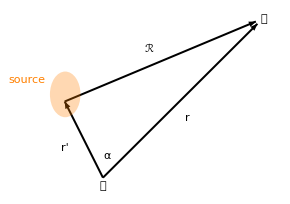

```mathematica
ClearAll["Global`*"];Graphics[{Thickness[0.005],Arrow[{{0,0},{-.5,1}}],Arrow[{{-.5,1},{2.,2.05}}],Arrow[{{0,0},{2.02,2.02}}],Style[Text["r'",{-.5,.4}],24,Bold],Style[Text["r",{1.1,.8}],24,Bold],Style[Text[ℛ,{.6,1.7}],24,Bold],Style[Text["α",{0.06,.3}],16],{Orange,Style[Text[source,{-1,1.3}],12],Opacity[0.3],Disk[{-.5,1.1},{.2,.3} ]},Style[Text["𝒫",{2.1,2.1}],18],Style[Text["𝒪",{0,-.1}],12]}]
```

1.3 Coulomb’s Law

The cornerstone of electrostatics is Coulomb's law,

coulombs law

which describes the force between two stationary charges q and Q separated by distance ℛ.

F=(q Q)/(4π  ("ε")_0 ℛ^2)ℛ̂ =(q Q ℛ)/(4π  ("ε")_0(ℛ\[Application]ℛ  )^(3/2))

Placing q (source) at location  r' and Q (observer) at location r gives the force F on Q.

Draw the diagram for the force on Q.

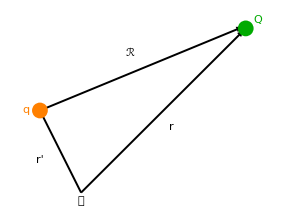

```mathematica
Graphics[{Style[Text["𝒪",{0,-.1}],12],Thickness[0.005],Arrow[{{0,0},{-.5,1}}],Arrow[{{-.5,1},{1.97,2.02}}],Arrow[{{0,0},{1.98,1.98}}],Style[Text["r'",{-.5,.4}],18,Bold],Style[Text["r",{1.1,.8}],18,Bold],Style[Text[ℛ,{.6,1.7}],18,Bold],{Orange,Style[Text[q,{-.67,1.}],16],Orange,PointSize[.04],Point[{-.5,1.} ]},Darker[Green],PointSize[.04],Point[{2.0,2}],Style[Text[Q,{2.15,2.1}],16]}]
```

Calculate the force vector on Q=1 μC at {1,0,0} m due to q=1 μC at {0,1,0} m.

```mathematica
q= 1 Quantity[, "Microcoulombs"]; Q= 1 Quantity[, "Microcoulombs"]; r={0,1,0}Quantity[, "Meters"]; r′={1,0,0} Quantity[, "Meters"]; ℛ=r-r′; N[UnitConvert[ (q Q ℛ)/(4π Quantity[, "ElectricConstant"](ℛ.ℛ  )^(3/2)), Quantity[, "Newtons"]],2]
```

{-0.0032 N,0.0032 N,0 N}

The force on q is a Newton’s 3rd law pair and is obtained by switching r and  r'.

Draw the diagram for the force on q.

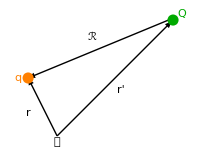

```mathematica
ClearAll["Global`*"];Graphics[{Style[Text["𝒪",{0,-.1}],12],Thickness[0.005],Arrow[{{0,0},{-.5,1}}],Arrow[{{1.97,2.02},{-.5,1}}],Arrow[{{0,0},{1.98,1.98}}],Style[Text["r",{-.5,.4}],18,Bold],Style[Text["r'",{1.1,.8}],18,Bold],Style[Text[ℛ,{.6,1.7}],18,Bold],{Orange,Style[Text[q,{-.67,1.}],16],Orange,PointSize[.04],Point[{-.5,1.} ]},Darker[Green],PointSize[.04],Point[{2.0,2}],Style[Text[Q,{2.15,2.1}],16]}]
```

1.3.1 Fundamental Strength

The force between two elementary charges gives the fundamental strength of the electric force.

Calculate the force between two charges  "e" at a distance of 1 nm in units of eV/nm.

```mathematica
UnitConvert[Quantity[, "ElementaryCharge"]^2/(4 π Quantity[, "ElectricConstant"] Quantity[, "Nanometers"]^2),Quantity[, ("Electronvolts")/("Nanometers")]]
```

1.43996455 eV/nm

The strength of the electric force is represented by

("e")^2/(4 π  ("ε")_0)≃1.44  "nm" "eV"

It can made dimensionless by normalizing to ℏ c, resulting in a historically significant number, the fine structure constant, that played such an important role during the birth of quantum physics.

Calculate the dimensionless strength of the electromagnetic force.

```mathematica
Rationalize[UnitConvert[Quantity[, "ElementaryCharge"]^2/(4 π Quantity[, "ElectricConstant"]Quantity[, "ReducedPlanckConstant"]Quantity[, "SpeedOfLight"])],10^-5]
```

1/137

This rational fraction is good to 1 part in 10^5.

The strength of the electromagnetic force is enormously greater than gravity.

Calculate the ratio of electric to gravity for an electron-proton interaction.

```mathematica
N[UnitConvert[(Quantity[, "ElementaryCharge"]^2/(4 π Quantity[, "ElectricConstant"]))/(Quantity[, "GravitationalConstant"] Entity["Particle","Proton"][EntityProperty["Particle","Mass"]]Entity["Particle","Electron"][EntityProperty["Particle","Mass"]])],1]
```

2.×10^39

1.3.2 Superposition

The superposition principle, that the interaction of any pair of charges does not depend on the existence of other nearby charges, is the most important concept in electromagnetism. Everything depends on it.

Calculate the force vector on charge  "e" at {1,0,0} nm due to charges  "e" at {0,1,0} nm and {0,-1,0} nm.

```mathematica
r={1,0,0} Quantity[, "Nanometers"]; r′={{0,1,0} Quantity[, "Nanometers"], {0,-1,0} Quantity[, "Nanometers"]};
N[UnitConvert[Sum[(Quantity[, "ElementaryCharge"]^2 ℛ)/(4π Quantity[, "ElectricConstant"](ℛ.ℛ )^(3/2)),{ ℛ,(r-#)&/@ r′}],Quantity[, ("Electronvolts")/("Nanometers")]],3]
```

{1.02 eV/nm,0 eV/nm,0 eV/nm}

The symbol  r′ represents a set of position vectors which are manipulated inside the sum.

```mathematica
Graphics[{Style[Text["𝒪",{-.05,-.05}],12],Thickness[0.005],Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{0,-1}}],Arrow[{{0,1},{1,0}}],Style[Text["r",{.5,-.1}],18,Bold],Style[Text["r'",{-.1,.5}],18,Bold],Style[Text[ℛ,{.62,.62}],18,Bold],{Orange,PointSize[.06],Point[{0,1.02} ],Point[{0,-1} ]},Darker[Green],PointSize[.06],Point[{1.04,0}]}]
```

-Graphics-

The superposition principle works for any number of charges.

Calculate the the electric force on a charge  "e" at {1,0,0} nm  from 100 other like charges  "e" at random positions {x,y,z} in the ranges 0 to 1 nm.

```mathematica
r={1,0,0} Quantity[, "Nanometers"];n=100;  r′=Table[RandomReal[{0,1},3] Quantity[, "Nanometers"],n];
F=UnitConvert[Sum[(Quantity[, "ElementaryCharge"]^2 ℛ)/(4π Quantity[, "ElectricConstant"](ℛ.ℛ )^(3/2)),{ ℛ,(r-#)&/@ r′}],Quantity[, ("Electronvolts")/("Nanometers")]]
```

{122.354 eV/nm,-108.64 eV/nm,-85.8239 eV/nm}

Make a 3D plot of the charge positions, labeling the observer charge in green.

```mathematica
Graphics3D[{Point[QuantityMagnitude/@r′]}~Join~{PointSize[.025],Darker[Green],Point[{1,0,0}]},PlotRange->{{0,1},{0,1},{0,1}},AxesLabel->{x,y,z},Axes->True]
```

-Graphics3D-

1.4 Electric Field

The concept of electric field is born as a consequence of the superposition principle. It is defined as a vector field that would produce a force q_0E on a charge q_0 placed in the field. Thus,

E=F/q_0

Note that the charge  q_0 is not part of the definition of E. It only plays the role of an observer (𝒫), like the “green-dot” charge in the previous example, which felt the field produced by the other 100 charges. For a point charge source (q),

E=q/(4π  ("ε")_0 ℛ^2)ℛ̂

Plot the electric field vector in the {x,y} plane from a point charge at the origin.

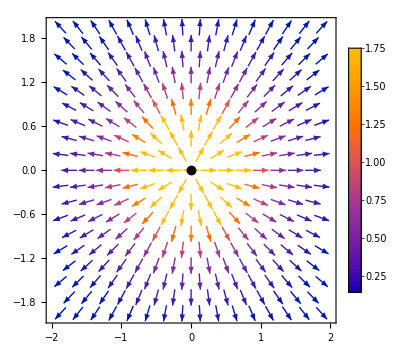

```mathematica
VectorPlot[{x,y}/((x^2+y^2)^(3/2)),{x,-2,2},{y,-2,2},PlotLegends->Automatic,Epilog->{PointSize[.02],Point[{0,0}]}]
```

The units of the electric field are N/C which we may also write in terms of the volt, the unit of electric potential (Section 1.7),  as  V/m.

Show that N/C = V/m.

```mathematica
Quantity[, ("Newtons")/("Coulombs")]==Quantity[, ("Volts")/("Meters")]
```

True

Calculate the electric field at {1,0,0} nm due to a charge  "e" at the origin.

```mathematica
ℛ={1  Quantity[, "Nanometers"],0  Quantity[, "Nanometers"],0  Quantity[, "Nanometers"]};N[UnitConvert[(Quantity[, "ElementaryCharge"]ℛ)/(4π Quantity[, "ElectricConstant"]( ℛ.ℛ)^(3/2)),Quantity[, ("Volts")/("Nanometers")]],3]
```

{1.44 V/nm,0 V/nm,0 V/nm}

The superposition principle can be used to calculate the electric field from any distribution of charge.

Calculate the electric field at the red dot due to the 100 random charges above.

```mathematica
UnitConvert[F/Quantity[, "ElementaryCharge"],Quantity[, ("Volts")/("Nanometers")]]
```

{122.354 V/nm,-108.64 V/nm,-85.8239 V/nm}

1.4.1 Linear Charge Density

A differential element of a linear charge distribution (charge per length = λ) is given by

𝕕q=λ 𝕕𝕝'

and the electric field for such a geometry can be calculated by adding up differential pieces of charge along the path.

E=1/(4π  ("ε")_0)∫ ⅆ𝕝'(λ(r))/ℛ^2 ℛ̂

Consider a straight-line charge segment from -L/2 to L/2.

Draw the line charge integration geometry.

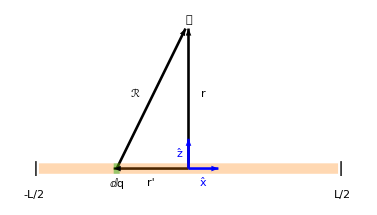

```mathematica
Graphics[{{Opacity[0.5],Green, Line[{{.25,0},{0.27,0}}]},Line[{{-0.01,-0.025},{-0.01,0.025}}],Line[{{1+0.01,-0.025},{1+0.01,0.025}}],Style[Text["r'",{0.375,-0.05}],18,Bold ],Style[Text["r",{0.55,0.25}],18,Bold ],Style[Text["ℛ",{0.32,0.25}],18,Bold],Style[Text["𝒫",{0.5,0.5}],12],Style[Text["-L/2",{-.015,-0.09}],12],Style[Text["L/2",{1.015,-0.09}],12],Style[Text["ⅆq",{0.26,-0.05}],12],{Thickness[0.005],Arrow[{{0.5,0},{0.5,0.47}}],Arrow[{{0.26,0},{0.49,0.47}}],Arrow[{{.5,0},{.25,0}}]},Thickness[0.02],{Opacity[0.3],Orange,Line[{{0,0},{1,0}}]},{Thickness[0.005],Blue,Arrow[{{0.5,0},{0.5,0.1}}],Style[Text[x̂,{0.55,-0.05}],12],Style[Text[ẑ,{0.47,0.05}],12],Arrow[{{0.5,0},{0.6,0}}]},{Opacity[0.4],Darker[Green], Line[{{.25,0},{0.27,0}}]}}]
```

Calculate the electric field vector at a distance z from the center of a line of charge with length L.

```mathematica
r={0,0,z}; r′={x′,0,0}; ℛ=r-r′; $Assumptions={L>0,z∈Reals,z≠0};
Ε=λ/(4π Subscript[ε, 0])∫_(-L/2)^(L/2) ℛ/( ℛ.ℛ)^(3/2)ⅆx′
```

{0,0,(L λ)/(2 π z √(L^2+4 z^2) ε_0)}

Take the limit (L->∞) to get the result for an infinite line of charge.

```mathematica
Limit[Ε,L->∞]//Quiet
```

{0,0,λ/(2 π z ε_0)}

We can easily get the field away from the z axis. All we have to do is change the observation point from (0, 0, z) to (x, 0, z). The field is symmetric in azimuth. Needless to say, this calculation would be time-consuming without Mathematica.

Draw the line charge integration geometry off the symmetry axis.

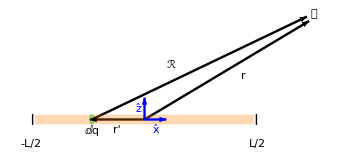

```mathematica
Graphics[{{Opacity[0.5],Green, Line[{{.25,0},{0.27,0}}]},Line[{{-0.01,-0.025},{-0.01,0.025}}],Line[{{1+0.01,-0.025},{1+0.01,0.025}}],Style[Text["r'",{0.375,-0.05}],18,Bold ],Style[Text["r",{.95,0.2}],18,Bold ],Style[Text["ℛ",{0.62,0.25}],18,Bold],Style[Text["𝒫",{1.27,0.48}],12],Style[Text["-L/2",{-.015,-0.11}],12],Style[Text["L/2",{1.015,-0.11}],12],Style[Text["ⅆq",{0.26,-0.05}],12],{Thickness[0.005],Arrow[{{0.5,0},{1.25,0.45}}],Arrow[{{0.26,0},{1.24,0.47}}],Arrow[{{.5,0},{.25,0}}]},Thickness[0.02],{Opacity[0.3],Orange,Line[{{0,0},{1,0}}]},{Thickness[0.005],Blue,Arrow[{{0.5,0},{0.5,0.1}}],Style[Text[x̂,{0.55,-0.05}],12],Style[Text[ẑ,{0.47,0.05}],12],Arrow[{{0.5,0},{0.6,0}}]},{Opacity[0.4],Darker[Green], Line[{{.25,0},{0.27,0}}]}}]
```

Calculate the electric field at  (x,0,z) from the same line of charge above.

```mathematica
ClearAll["Global`*"];r={x,0,z}; r′={x′,0,0}; ℛ=r-r′; $Assumptions={L>0,z∈Reals,z≠0,x∈Reals};
Ε=λ/(4π Subscript[ε, 0])∫_(-L/2)^(L/2) ℛ/( ℛ.ℛ)^(3/2)ⅆx′//Together//FullSimplify
```

{((-√((L-2 x)^2+4 z^2)+√((L+2 x)^2+4 z^2)) λ)/(2 π √(L^4+8 L^2 (-x^2+z^2)+16 (x^2+z^2)^2) ε_0),0,((2 x (√((L-2 x)^2+4 z^2)-√((L+2 x)^2+4 z^2))+L (√((L-2 x)^2+4 z^2)+√((L+2 x)^2+4 z^2))) λ)/(4 π z √(L^4+8 L^2 (-x^2+z^2)+16 (x^2+z^2)^2) ε_0)}

Note that Latin E is reserved for the exponent function. Greek Ε is used here.

Calculate the electric field for L=0.1 "m", x=0.4  "m", z=.3  "m", and λ= 1  "μC"/ "m".

```mathematica
Ε[[2]]=0 Quantity[, "Volts"]/Quantity[, "Meters"]; UnitConvert[Ε,Quantity[, "Volts"]/Quantity[, "Meters"]]/. {L->0.1 Quantity[, "Meters"], x->0.4 Quantity[, "Meters"],z ->.3 Quantity[, "Meters"], λ-> 1 Quantity[, "Microcoulombs"]/Quantity[, "Meters"],Subscript[ε, 0]->Quantity[, "ElectricConstant"]}
```

{2878.75 V/m,0 V/m,2180.79 V/m}

We can readily check that we reproduce the previous answer when x → 0. It is always a good idea to check a complicated answer in the appropriate limit.

Expand Ε in a series around x→0 to get the finite-line result.

```mathematica
Ε[[2]]=0;Simplify[Series[Ε,{x,0,0}],{z>0}]
```

{O[x]^1,0,(L λ)/(2 π z √(L^2+4 z^2) ε_0)+O[x]^1}

Take the limit as L→∞ to get the infinite-line result. .

```mathematica
Limit[Ε,L->∞]//Quiet
```

{0,0,λ/(2 π z ε_0)}

Plot the electric field vector from a line charge -1 < x < 1 and  indicate the location of the line of charge.

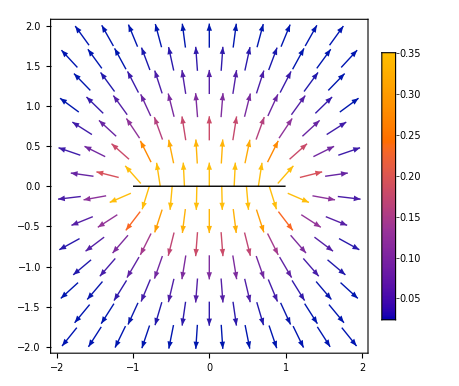

```mathematica
VectorPlot[Ε[[{1,3}]]/.{L->2,λ->1,Subscript[ε, 0]->1},{x,-2,2},{z,-2,2},PlotLegends->Automatic,VectorPoints->12,Epilog->Line[{{-1,0},{1,0}}]]
```

1.4.2 Surface Charge Density

A differential element of a surface charge distribution (charge per area = σ) is given by

𝕕q=σ 𝕕𝕒'

and the electric field is given by surface integration.

E=1/(4π  ("ε")_0)∫ ⅆ𝕒'(σ(r))/ℛ^2 ℛ̂

Square Geometry

Find the electric field a distance z (on axis) from the center of a square of charge, with dimension (2L, 2L) in the x-y plane:

```mathematica
ClearAll["Global`*"];r={0,0,z}; r′={x′,y′,0}; ℛ=r-r′;$Assumptions={z∈Reals,L>0,z≠0};
Ε= σ/(4π Subscript[ε, 0])∫_-L^L ∫_-L^L ℛ/( ℛ.ℛ)^(3/2)ⅆx′ⅆy′//FullSimplify
```

{0,0,(σ ArcCot[(z √(2 L^2+z^2))/L^2])/(π ε_0)}

Draw the square of charge.

```mathematica
ClearAll["Global`*"];Graphics3D[{Style[Text["ẑ",{0,-0.1,1.14}],14],Style[Text["𝒫",{0,.04,2.05}],14],Style[Text[L,{0,-.6,1}],12],Style[Text[L,{.6,0,1}],12],Style[Text["ⅆq",{0.29,.29,1}],14],Style[Text["ℛ",{0,.5,1.5}],18,Bold],Style[Text["r'",{0,.2,.9}],18,Bold],Style[Text["r",{0,-.1,1.6}],18,Bold],Line[{{0,0,1},{0,0,2}}],Thickness[.005],Arrow[{{0,0,1},{0,0,2}}],Thickness[0.005],Arrow[{{0,0,1},{0,0,1.3}}],Arrow[{{0,0,1},{.2,.2,1}}],Arrow[{{0.2,.2,1},{0,0.05,2}}],Opacity[0.3],Orange,Cuboid[{-.5,-.5,1},{.5,.5,1.001}],Darker[Green],Cuboid[{.15,.15,1},{.25,.25,1.001}]},Boxed->False]
```

-Graphics3D-

Find the leading order term at small z.

```mathematica
Simplify[Series[Ε,z->0],{z>0}]
```

{0,0,σ/(2 ε_0)+O[z]^1}

At small z, the square appears as an infinite plane, and the electric field becomes

E =σ/(2 ε_0)ẑ

This is an important result.

Find the leading order term for large z/L.

```mathematica
Simplify[Series[Ε,{L,0,2}],{z>0}]/.σ->Q/(2L)^2
```

{0,0,Q/(4 π z^2 ε_0)}

At large z we recover the electric field for a point charge of magnitude

σ=Q/(2L)^2

Disk Geometry

The field from a disk of charge is useful because it can be used to build other geometries such as a ball or cone.

Draw the disk geometry.

```mathematica
ClearAll["Global`*"];Graphics3D[{Style[Text["ϕ'",{0.15,0.05,1}],12],Style[Text["𝒫",{0,.04,2.05}],14],Style[Text[ⅆq,{0.29,.29,1}],14],Style[Text["ℛ",{0.25,-.3,1.7}],18,Bold],Style[Text["r'",{.04,.24,1}],18,Bold],Style[Text["r",{-.05,-.1,1.6}],18,Bold],Line[{{0,0,1},{0,0,2}}],Thickness[.005],Arrow[{{0,0,1},{0,0,2}}],{Blue,Style[Text["x̂",{0.25,-.1,1}],14],Style[Text["ẑ",{-.15,0.1,1.14}],14],Thickness[0.005],Arrow[{{0,0,1},{0,0,1.3}}],Arrow[{{0,0,1},{0.3,0,1}}]},Arrow[{{0,0,1},{.2,.2,1}}],Arrow[{{0.2,.2,1},{0,0.05,2}}],Opacity[0.3],Orange,Cylinder[{{0,0,1},{0,0,1.001}},.7],Darker[Green],Cylinder[{{0.2,.2,1},{0.2,.2,1.001}},.03]},Boxed->False]
```

-Graphics3D-

Set up the polar coordinates for integration over the disk.

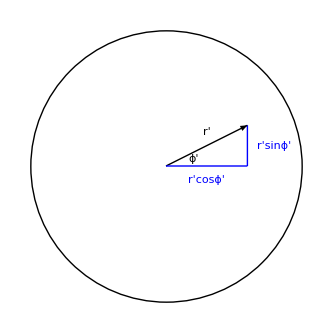

```mathematica
Graphics[{Circle[],Style[Text["r'",{.3,.25}],18], Style[Text["ϕ'",{.2,.05}],12],Arrow[{{0,0},{.6,.3}}],Blue,Line[{{0,0},{.6,0}}],Line[{{.6,0},{.6,.3}}],Style[Text["r'cosϕ'",{.3,-.1}],18],Style[Text["r'sinϕ'",{.8,.15}],18]}]
```

Find the electric field a distance along the symmetry axis of a disk of charge of radius R in the x-y plane.

```mathematica
r= {0,0,z}; r′= s′{Cos[ϕ′],Sin[ϕ′],0}; ℛ= r-r′;$Assumptions={R>0,z∈Reals,z>0};
Ε= σ/(4π Subscript[ε, 0])∫_0^(2π) ∫_0^R s′ ℛ/( ℛ.ℛ)^(3/2)ⅆs′ⅆϕ′//FullSimplify
```

{0,0,(σ-(z σ)/(√(R^2+z^2)))/(2 ε_0)}

Note that the integration variable is a dummy and we can call it whatever we want. We have already used r′ for the vector and we can’t use the same symbol again for its magnitude, so we used s′.

Find the leading order term at small z.

```mathematica
Simplify[Series[Ε,z->0],{z>0}]
```

{0,0,σ/(2 ε_0)+O[z]^1}

Again, it is observed that the field goes to σ/(2 ε_0)ẑ  at small z.

1.4.3 Volume Charge Density

A differential element of a volume charge distribution (charge per volume ρ) is given by

𝕕q=ρ 𝕕𝕍'

and the electric field is

E=1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r))/ℛ^2 ℛ̂

We may use the disk formula to calculate the field due to a uniform ball of charge at a distance r from the center by dividing the ball into disks. In the disk formula above,

σ=ρ 𝕕z',	z=r-z',		R_disk→√(R_ball-z'^2)

where z' is our integration variable from -R_ball to R_ball. A differential piece of the field is

𝕕E=1/(2 ε_0)ρ 𝕕z'(1-(r-z')/(√(R^2-z'^2+(r-z')^2))) r̂

and the field is given by

E =1/(2 ε_0)ρ (∫_-R)^R(1-(r-z')/(√(R^2-z'^2+(r-z')^2)))r̂ 𝕕z'

Draw the geometry for dividing the ball into disks.

```mathematica
Graphics3D[{Opacity[.7],Orange,Cylinder[{{3,3,2},{3,3,2.001}},Sqrt[5]], Green,Opacity[.3],Sphere[{3,3,0},3],Thickness[0.007],Black,Opacity[1],Line[{{3,3,0},{3+Sqrt[5],3,2}}],Arrow[{{3,3,0},{3,3,2}}],Line[{{3,3,2},{3+Sqrt[5],3,2}}],Arrow[{{3,3,0},{3,3,4}}],Text["R",{4.5,3,.8}],Text["z'",{2.8,3,1}],Text["r",{2.7,3,3.5}],Text["√(R^2)",{4,3,2.3}],Text["𝒫",{3,3,4.3}]},Boxed->False]
```

-Graphics3D-

Calculate the electric field outside a uniform ball of charge.

```mathematica
ClearAll["Global`*"];$Assumptions={𝓏∈Reals,𝓏>0,r∈Reals,r>R, R>0}; ρ=Q/((4/3)π R^3);ρ/(2 Subscript[ε, 0])∫_-R^R (1-(r-𝓏)/(√(R^2-𝓏^2+(r-𝓏)^2)))ⅆ𝓏
```

Q/(4 π r^2 ε_0)

This is a remarkable result. The field outside the ball of charge is identical to that of a point charge at the center.

We can use the same disk formula to get the field inside the ball. This time we need to divide the ball into two regions,  z' < r  (positive contribution) and z' > r  (negative contribution). For the positive contribution (integral -R to r) we may reverse the limits and introduce a minus sign.

Calculate the electric field inside a uniform ball of charge.

```mathematica
$Assumptions={𝓏∈Reals,r>0,r∈Reals,r<R, R>0}; ρ=Q/((4/3)π R^3);Simplify[-ρ/(2 Subscript[ε, 0])∫_r^R (1-(𝓏-r)/(√(R^2-𝓏^2+(r-𝓏)^2)))ⅆ𝓏-ρ/(2 Subscript[ε, 0])∫_r^-R (1-(r-𝓏)/(√(R^2-𝓏^2+(r-𝓏)^2)))ⅆ𝓏]
```

(Q r)/(4 π R^3 ε_0)

Noting that the charge inside a ball of radius r (the observation point) is

Q_in=4/3 π r^3 ρ=Q r^3/R^3

we see that

E=Q_in/(4π ("ε")_0 r^2)r̂

This yields another remarkable result, that the portion of charge that was radially greater than r gave zero contribution. By superposition, the electric field anywhere inside a uniform shell of charge is zero.

1.5 Electric Flux and Gauss’s Law

The electric flux (Φ) through a surface is defined by the integral

Φ=∫ E\[Application]ⅆ𝕒

where the vector element 𝕕𝕒 = n̂ 𝕕𝕒, with n̂ the unit vector normal to the surface and 𝕕𝕒  the differential area element. If the surface is closed, the direction of n̂ is outward. For a closed spherical surface, the flux from a charge inside is everywhere positive while the flux from a charge outside has both positive and negative contributions.

```mathematica
Graphics3D[{ Orange,Cylinder[{{0,√3,√3},{0,√3+0.001,√3+0.001}},0.2],Green,Opacity[.3],Sphere[{0,0,0},3],Black, Opacity[1],Arrow[{{0,√3,√3},{0,√3+1.5,√3+1.5}}],Style[Text[n̂,{0,√3+1.8,√3+1.8}],16,Bold],Style[Text[ⅆ𝕒,{.6,√3,√3}],16,Bold]},Boxed->False]
```

-Graphics3D-

1.5.1 Electric Field Lines

The concept of electric field lines is useful to visualize electric flux. Electric field lines always start and end on charges (which may be at infinity) because electric charge is the only source of the field. Electric field lines are drawn by connecting the arrows in a vector field plot. The relative strength of the field is given by the density of the field lines. Flux through a surface is represented by the number of lines passing through the surface. There is no convention for how many lines to draw except to draw enough to visualize the field clearly and to not distort the vector direction. Beware that a 2-dimensional plot, while often very useful, can hide the 3D-features.

Draw field lines in the {x,y} plane for a point charge.

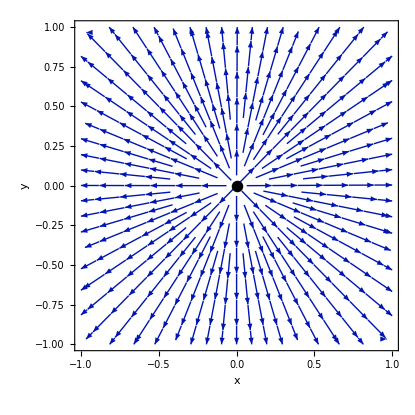

```mathematica
With[{n=1}, StreamPlot[{x,y}/((x^2+y^2)^(3/2)),{x,-n,n},{y,-n,n},]]
```

It can also be helpful to use color to show relative strength of the field. Notice that where the field lines are closer together, the magnitude of the vector field is greater.

Draw the field lines in 3D for a point charge.

```mathematica
With[{n=4}, StreamPlot3D[{x,y,z}/((x^2+y^2+z^2)^(3/2)),{x,-n,n},{y,-n,n},{z,-n,n},]]
```

-Graphics3D-

Flux Through a Sphere

We begin with the simplest of all flux calculations, that of a point charge at the center of a sphere. The unit normal to the sphere is just r̂ — the same as the direction of the electric field, so

E\[Application]ⅆ𝕒=E𝕕𝕒=q/(4π ε_0)r^2 sinθ 𝕕θ𝕕ϕ

Calculate the electric flux through a sphere of radius r from a point charge at the center.

```mathematica
ClearAll["Global`*"];1/(4 π Subscript[ε, 0])∫_0^(2π) ∫_0^π (r^2 Sin[θ]q)/r^2 ⅆθⅆϕ
```

q/ε_0

Now move the charge off-center to some random position inside the ball encompassed by the sphere and recalculate the flux.

Calculate the electric flux through a sphere of unit radius from a point charge q off center at a random inside position.

```mathematica
𝓇=RandomPoint[Ball[]]; 
 r={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};ℛ=r-𝓇; NIntegrate[(Sin[θ] ℛ.r)/(√(ℛ.ℛ)ℛ.ℛ),{θ,0,π},{ϕ,0,2π}] q/(4 π Subscript[ε, 0])
```

(1. q)/ε_0

The flux did not change. The charge can be anywhere inside the sphere and the answer is q/ ("ε")_0. Explore what happens when the charge is outside the sphere. In this case, every electric field line that enters the sphere (negative flux contribution) must also exit (positive flux contribution).

Draw the field lines from a charge outside a sphere.

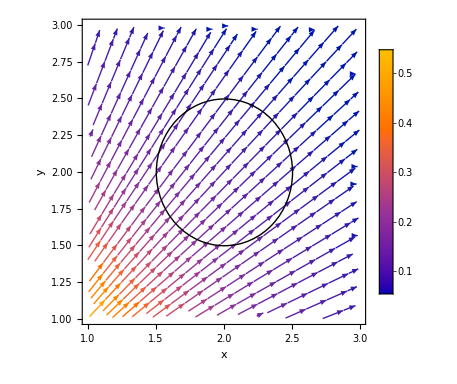

```mathematica
StreamPlot[{x,y}/((x^2+y^2)^(3/2)),{x,1,3},{y,1,3},]
```

Draw the field lines in 3D from a charge outside a sphere.

```mathematica
Show[StreamPlot3D[{x,y,z}/(x^2+y^2+z^2),{x,1,3},{y,1,3},{z,1,3},],Graphics3D[{Opacity[.3],Green,Sphere[{2,2,2},.5]}]]
```

-Graphics3D-

Calculate the electric flux through a sphere of unit radius from a point charge q outside the sphere.

```mathematica
ClearAll["Global`*"]; 𝓇=RandomReal[{1,2},3]; 
 r={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};ℛ=r-𝓇;q/(4 π Subscript[ε, 0]) NIntegrate[(Sin[θ] ℛ.r)/(√(ℛ.ℛ)ℛ.ℛ),{θ,0,π},{ϕ,0,2π}]//Quiet//Chop
```

0

Numerical integration will issue a warning when converging to 0 (Quiet removes the warning) and Chop rounds off a number that is zero within accuracy of 10^-10.

The flux is seen to be zero when there is no charge inside. Only charges inside the sphere can contribute to the flux. By superposition, this is true for any number of charges. Similarly, it is true for any closed surface that only charges inside contribute to a net flux through the surface.

Flux Through a Cube

As another example, take a point charge q at one corner {0,0,0} of a cube. Consider the electric flux though one opposing face of the cube.

Draw the flux though one face of a cube from a charge at its corner.

```mathematica
Show[StreamPlot3D[{x,y,z}/((x^2+y^2+z^2)^(3/2)),{x,0,1.1},{y,0,1.1},{z,0,1.1},AxesLabel->{x,y,z},RegionBoundaryStyle->None,PlotLegends->Automatic,ImageSize->Medium,StreamMarkers->"Arrow3D"],Graphics3D[{Black,PointSize[0.03],Point[{0,0,0}],Opacity[.3],Green,Cuboid[{1,0,0},{1.0001,1,1}]}]]
```

-Graphics3D-

Calculate the electric flux through one opposing face of the cube.

```mathematica
ClearAll["Global`*"] ; $Assumptions={y∈Reals,y>0,z∈Reals,z>0,a∈Reals,a>0};r={a,y,z}; n={1,0,0};  f[y_]=q/(4π Subscript[ε, 0])Integrate[(r.n)/(Norm[r]r.r),y];  g[z_]=Integrate[f[a]-f[0],z];FullSimplify[ g[a]-g[0]]
```

q/(24 ε_0)

If we build up a larger cube with 8 of the original cubes (2×2×2), with the point charge at the center, we can see that there are now 24 faces of the area of the original cube faces. The flux through each is the same by symmetry. The total flux through the enclosed surface has to be q/ ("ε")_0, so the flux through each face is q/(24  ("ε")_0).

Electric Field Lines from Three charges

The superposition principle is demonstrated  in this example of the electric field lines from 3 point charges. The size and signs of the charges are variable as are the positions which may be dragged.

```mathematica
(Column[{#1[EntityProperty["WolframDemonstration","WolframDemonstrationsLink"]]/.Hyperlink[link_]:>Hyperlink[#1[EntityProperty["WolframDemonstration","Name"]],link],Row[Join[{"By: "},Riffle[(Hyperlink[#1["Name"],First[#1["ContributorLink"]]]&)/@#1[EntityProperty["WolframDemonstration","Authors"]],", "]]],}]&)[Entity["WolframDemonstration","ElectricFieldsForThreePointCharges"]]
```

[Electric Fields for Three Point Charges ](https://demonstrations.wolfram.com/ElectricFieldsForThreePointCharges)
By: [S. M. Blinder](http://demonstrations.wolfram.com/author.html?author=S.+M.+Blinder)

```mathematica
Manipulate[Show[Quiet@StreamPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],q2]+EX[x,y,Q3[[1]],Q3[[2]],q3],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],q2]+EY[x,y,Q3[[1]],Q3[[2]],q3]},{x,-20,20},{y,-15,15},AspectRatio->.75],Graphics[{RGBColor[{Boole[q1<0],0,0}],Opacity[Sign[Abs[q1]]],Thick,Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Opacity[Sign[Abs[q2]]],Thick,Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Opacity[Sign[Abs[q3]]],Thick,Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}]
}],ImageSize->{575,375}],
{{q1,-1,"q_1"},-2,2,.1,Appearance->"Labeled"},
{{q2,2,"q_2"},-2,2,.1,Appearance->"Labeled"},
{{q3,-1,"q_3"},-2,2,.1,Appearance->"Labeled"},{{Q1,{-10,0}},{-20,-15},{20,15},Locator,Appearance->None},{{Q2,{0,0}},{-20,-15},{20,15},Locator,Appearance->None},{{Q3,{10,0}},{-20,-15},{20,15},Locator,Appearance->None},ContinuousAction->False,TrackedSymbols:>True,Initialization:>(EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2));EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2)))]
```

1.5.2 Gauss’s Law

For a closed surface, the electric flux does not depend on the size or shape of the surface, rather only on the amount of charge that is inside (q_in).

∮  E· ⅆ𝕒= q_in/(("ε")_0)

This is the integral form of Gauss’s law, one of the 4 Maxwell equations. Gauss’s law has only limited calculational value in this form, requiring symmetry to compute the flux, but it has tremendous conceptual value, serving as an invaluable bridge between vector calculus and electromagnetism. The law is complete and will require no revision. It shall be put in differential form shortly.

Cylindrical Geometry

We shall begin with a problem that we know the answer to, the field due to a line of charge of length L and linear charge density λ, where r is the shortest distance to the charge.

E=(L λ)/(2 π r √(L^2+4 r^2)ε_0)

Take the limit as L → ∞.

```mathematica
ClearAll["Global`*"] ; Limit[(L λ)/(2 π r √(L^2+4 r^2) Subscript[ε, 0]),L->∞]
```

λ/(2 π r ε_0)

To use Gauss’s law to calculate a field, we need to be able to express the flux in terms of the field, for which we need symmetry. The first step is to visualize the symmetry and define a closed surface for the flux calculation. The symmetry in this case is that the field direction is radial. The answer to the flux is obtained by adding up the charge inside the surface and then equating the two expressions in Gauss’s law to solve for E. For the line of charge, our chosen surface is a concentric cylinder of radius r and length L. The radius is the distance at which we are calculating the field and may be treated as a variable. The length L does not matter, it will cancel out.

Draw a Gaussian surface (green) for a long line of charge (orange).

```mathematica
Graphics3D[{Orange,Thickness[0.01],Line[{{-10,0,0},{10,0,0}}], Green,Opacity[.3],Cylinder[{{-1,0,0},{1,0,0}},3],Opacity[1],Black,Arrow[{{0,0,3},{0,0,5}}],Text["E",{0,0,5.4}]},Boxed->False]
```

-Graphics3D-

The flux is non-zero only on the curved part of the cylinder (no E field lines pass though the flat ends).

∮  E· ⅆ𝕒= E (2 π r L)=q_in/(("ε")_0)=λL/(("ε")_0)

Solve for E:

E =λ/(2 π r ("ε")_0)

The direction is radial which we had to know in order to write the expression for the flux in terms of E at the outset.

We can now easily calculate E from a cylinder of charge using the same technique. It does not matter if r is inside or outside the cylinder. It also does not matter if the charge density is not uniform, as long as it varies only radially.

Planar Geometry

For an infinite plane of charge (density σ) we also calculated the field and found

E =σ/(2 ("ε")_0)

with the direction perpendicular to the plane. This time our Gaussian surface is a cylinder that is oriented along the direction of the field. We could also use a rectangular shape. There is flux only through the flat ends. Let the radius of the cylinder be d.

∮  E· ⅆ𝕒= E (2 π d^2 )=q_in/(("ε")_0)=(σ π d^2)/(("ε")_0)

Solve for E:

E =σ/(2 ("ε")_0)

and its direction is away from the plane on both sides.

Draw a Gaussian surface (green) for a plane of charge (orange).

```mathematica
Graphics3D[{Orange,Polygon[{{0,0,0},{10,0,0},{10,10,0},{0,10,0}}], Green,Opacity[.3],Cylinder[{{5,5,-2},{5,5,2}},2],Thickness[0.007],Black,Opacity[1],Arrow[{{5,5,2},{5,5,4}}],Arrow[{{5,5,-2},{5,5,-4}}],Text["E",{5,5,4.3}],Text["E",{5,5,-4.3}]},Boxed->False]
```

-Graphics3D-

Spherical Geometry

For a ball of charge (radius R and density ρ) we found the field outside to be

E =(ρ R^3)/(3 ("ε")_0 r^2)

Let the radius of the Gaussian sphere be our variable r.

∮  E· ⅆ𝕒= E (4 π r^2 )=q_in/(("ε")_0)=(ρ(4/3 π R^3))/(("ε")_0)

Solve for E:

E =(ρ R^3)/(3 ("ε")_0 r^2)

The direction of E is radial.

Draw a Gaussian surface (green) for a ball of charge (orange).

```mathematica
Graphics3D[{Orange,Sphere[], Green,Opacity[.3],Sphere[{0,0,0},3],Opacity[1],Thickness[0.005],Black,Arrow[{{0,0,3},{0,0,4}}],Text["E",{0,0,4.2}]},Boxed->False]
```

-Graphics3D-

Inside the ball we have

∮  E· ⅆ𝕒= E (4 π r^2 )=q_in/(("ε")_0)=(ρ(4/3 π r^3))/(("ε")_0)

Solve for E:
		E =(ρ r)/(3 ("ε")_0)

Draw the Gaussian surface (green) inside the ball (orange).

```mathematica
Graphics3D[{Opacity[.3],Orange,Sphere[], Green,Sphere[{0,0,0},0.4],Opacity[1],Thickness[0.005],Black,Arrow[{{0,0,.4},{0,0,.8}}],Text["E",{0,0,.85}]},Boxed->False]
```

-Graphics3D-

We can readily expand the line charge to a cylinder and the plane of charge to a thin cuboid.

Draw a Gaussian surface (green) for a long cylinder of charge (orange).

```mathematica
Graphics3D[{Orange,Cylinder[{{-10,0,0},{10,0,0}},1], Green,Opacity[.3],Cylinder[{{-1,0,0},{1,0,0}},3],Thickness[0.005],Opacity[1],Black,Arrow[{{0,0,3},{0,0,5}}],Text["E",{0,0,5.4}]},Boxed->False]
```

-Graphics3D-

Draw a Gaussian surface (green) for a thin cuboid of charge (orange).

```mathematica
Graphics3D[{Orange,Cuboid[{0,0,0-.3},{10,10,.3}], Green,Opacity[.3],Cylinder[{{5,5,-2},{5,5,2}},2],Thickness[0.007],Black,Opacity[1],Arrow[{{5,5,2},{5,5,4}}],Arrow[{{5,5,-2},{5,5,-4}}],Text["E",{5,5,4.3}],Text["E",{5,5,-4.3}]},Boxed->False]
```

-Graphics3D-

1.6 Divergence and Curl

A vector plot of the electric field from a point charge shows a dramatic divergence. This is due to the fact that electric field lines start and end on charges. The charges are the only source of the field.

Made a 3D plot of the electric field vector from a point charge.

```mathematica
StreamPlot3D[{x, y,z}/((x^2+y^2+z^2)^(3/2)),{x,-3,3},{y,-3,3},{z,-3,3}, ]
```

-Graphics3D-

1.6.1 Divergence of a Point-Charge Field

The r̂/r^2 field dependence of a point charge deserves special attention. See Appendix C on index notation.

∇\[Application](r̂)/r^2=∂_j [r_j(r_k r_k)^(-3/2)]=(∂_j r_j)/r^3+r_j(-3/2)(2 r_k∂_j r_k)/r^5=3/r^3-3/r^3=0

Calculate Div r̂/r^2.

```mathematica
ClearAll["Global`*"];Div[{1/r^2,0,0},{r,θ,ϕ},"Spherical"]
```

0

The answer is zero. What went wrong? Actually, the divergence is zero EXCEPT at the origin where there is an infinity. Using a point charge at the origin inside a sphere

∮ ⅆ𝕒 \[Application](r̂)/r^2=4π=∫ ⅆ𝕍∇\[Application](r̂)/r^2

If the volume integral is going to match the 4π from the flux calculation, then the infinity from the divergence must be a delta function that integrates to 4π.

∇\[Application](r̂)/r^2=4π δ(r) 		∫ ⅆ𝕍δ(r)=1

Now we can see that

∇\[Application]E = ρ/(("ε")_0)

The divergence of the electric field is zero everywhere except where there is charge and then it is a delta function.

1/(("ε")_0)∫ρⅆ𝕍=q_in/(("ε")_0)

The divergence of E tells us where the source charge is located. For a point charge q at the origin, we have

∇\[Application]E = q/(("ε")_0)δ(r)

In other words,

ρ= qδ(r)

such that when integrated over any volume that contains the charge gives

∫ρ𝕕𝕍=q

Thus

4π r^2  E = q/(("ε")_0)

and

E = q/(4π  ("ε")_0 r^2)r̂

The divergence of r̂/r^2 is therefore

∇\[Application] (r̂)/r^2=4π δ^3(r)

1.6.2 Curl of  a Point-Charge Field

The divergence example of the point charge should teach you to be cautious about interpreting the divergence of a vector field from a plot or from an equation. For the divergence, the field depends on r in the r̂ direction. In the case of the curl, the field does not have components along θ̂ or ϕ̂. The curl is zero.

(∇×(r̂)/r^2)_k=ε_ijk∂_i [r_j(r_p r_p)^(-3/2)]=ε_ijk r_j∂_i (r_p r_p)^(-3/2)=ε_ijk r_j(-3/2)2 r_p∂_i r_p=ε_ijk(-3/r^5)r_i r_j=0

The last step can be seen to hold by switching i and j where ε_jik changes sign.

Calculate Curl r̂/r^2.

```mathematica
Curl[{1/r^2,0,0},{r,θ,ϕ},"Spherical"]
```

```mathematica
{0,0,0}
```

Alternately,

```mathematica
Curl[{x,y,z}/((x^2+y^2+z^2)^(3/2)),{x,y,z}]
```

{0,0,0}

Using superposition, we see that the curl of any electric field produced by static charges is zero.

∇×E=0

By Stokes' theorem,

∫ ∇×E⋄ⅆ𝕒=∮ E\[Application]ⅆ𝕝=0

The line integral of E around a closed loop is zero. This means that the line integral does not depend on the path — i.e. the electric field due to static charges is said to be conservative.

Only differences in potential matter.

ΔV=∫ E\[Application]ⅆ𝕝

1.7 Electric Potential

The independence of the line-integral of E on the path allows us to define the concept of electric potential. Suppose in some region we have a non-zero electric field.  A “test charge” would experience an electric force and would have a change in electric potential energy with position which is independent of the path taken. The change in potential energy per test charge is the electric potential. The units are the volt and the electric potential is commonly referred to as the voltage difference with respect to some reference point (ground).

The curl of the gradient of any scalar function is zero.

```mathematica
With[{V={f[x,y,z],g[x,y,z],h[x,y,z]}}, Curl[ Grad[V,{x,y,z}],{x,y,z} ]]
```

0

This allows us to define the electric potential V as the scalar function whose negative gradient gives E. The minus sign is necessary because a step in the direction of E reduces the potential.

E=-∇V

The electric potential for a point charge is given by the line integral of the field. Only differences in potential (ΔV) are physically meaningful. We can place the zero point at any position or add a constant to V. When we write V for the potential, as opposed to ΔV, we are referencing it with respect to our defined zero. This is usually (but not always) at infinity.

Calculate the electric potential due to a point charge at distance r from the origin.

```mathematica
$Assumptions={r∈Reals, r>0}; V=-q/(4π Subscript[ε, 0])∫_∞^r 1/𝓇^2 ⅆ𝓇
```

q/(4 π r ε_0)

Calculate the electric field.

```mathematica
-Grad[V,{r,θ,ϕ},"Spherical"]
```

{q/(4 π r^2 ε_0),0,0}

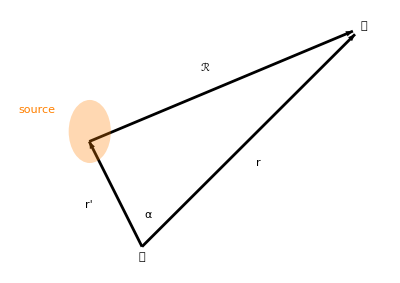

Superposition gives

E=1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r'))/ℛ^2 ℛ̂

The electric field has no curl (static case). Note that ρ does not depend on the coordinate r.

```mathematica
$Assumptions={x∈Reals,y∈Reals,z∈Reals,x′∈Reals,y′∈Reals,z′∈Reals};
ℛ={x,y,z}-{x′,y′,z′};
FullSimplify[ℛ/Norm[ℛ]^2{x,y,z}]
```

{0,0,0}

Using

∇1/ℛ=-(ℛ̂)/ℛ^2

gives

E=-∇[1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r'))/ℛ]

and

V=1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r'))/ℛ

relative to a zero at infinity. The line integral “undoes” the gradient (see this by writing out the three components)

ΔV=V_b-V_a=-∫_a^b E\[Application]ⅆ𝕝

Stokes theorem guarantees that the change in potential does not depend on the integration path, a property of zero curl.

1.7.1 Disk of Charge

Consider a disk of uniform surface charge density σ. We want to calculate the potential on the edge of the disk.  The problem is conceptually straight forward, but the integral is particularly nasty for a simple geometry.

V=σ/(4π ε_0)∫_0^(2π) ⅆφ∫_0^R ⅆr' r'/ℛ

Draw the geometry for the disk integration.

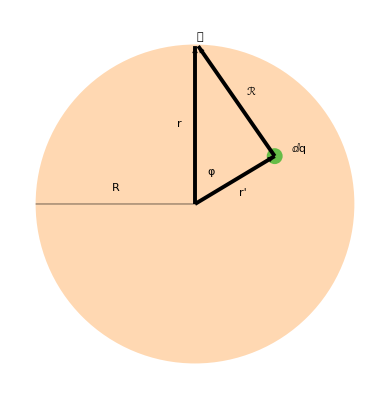

```mathematica
Graphics[{Opacity[0.3],Orange,Disk[],Opacity[0.6],Darker[Green],Disk[{.5,.3},.05],Opacity[1],Black,Style[Text["r",{-.1,0.5}],16,Bold],Style[Text["r'",{.3,0.07}],16,Bold],Style[Text["𝒫",{0.03,1.05}],16],Style[Text["ℛ",{.35,.7}],16,Bold],Style[Text["ⅆq",{.65,.35}],16],Style[Text["R",{-.5,.1}],16],Style[Text["φ",{.1,.2}],12],Thickness[0.007],Arrow[{{0,0},{0,0.99}}],Arrow[{{0,0},{.5,.3}}],Arrow[{{.5,.3},{0.02,0.99}}],Thickness[0.001],Line[{{0,0},{-1,0}}]}]
```

Calculate the potential at the edge of a disk of uniform surface charge density.

```mathematica
ClearAll["Global`*"]; $Assumptions={R∈Reals,R>0,𝓈∈Reals,𝓈>0,φ ∈Reals, φ>0};r={0,R,0}; r′=𝓈{Sin[φ],Cos[φ],0}; ℛ=(r-r′);
σ/(4π Subscript[ε, 0])∫_0^(2π) ∫_0^R 𝓈/(√(ℛ.ℛ))ⅆ𝓈ⅆφ//FullSimplify
```

(R σ)/(π ε_0)

Ring of charge:  on axis

```mathematica
Graphics3D[{{Opacity[1],Thickness[0.01],Orange,ResourceFunction["Circle3D"][{0,0,1},{1,1},π/2]},Style[Text["ẑ",{0,-0.1,2.8}],14],Style[Text["r'",{.1,0,1.5}],18,Bold],Style[Text["ℛ",{0,.5,1.6}],18,Bold],Arrow[{{0,0,1},{0,0,2}}],Arrow[{{0,1,1},{0,0,2}}],Thickness[.005],Thickness[0.005],Arrow[{{0,0,2.5},{0,0,2.8}}],,},Boxed->False]
```

-Graphics3D-

V=Q/(4π ε_0 ℛ)

For a disk of charge on axis, divide into rings.

```mathematica
Graphics3D[{{Opacity[1],Thickness[0.01],Orange,Cylinder[{{0,0,1},{0,0,1.001}},1]},Style[Text["ẑ",{0,-0.1,2.8}],14],Style[Text["r'",{.1,0,1.5}],18,Bold],Style[Text["ℛ",{0,.5,1.6}],18,Bold],Arrow[{{0,0,1},{0,0,2}}],Arrow[{{0,1,1},{0,0,2}}],Thickness[.005],Thickness[0.005],Arrow[{{0,0,2.5},{0,0,2.8}}],,},Boxed->False]
```

-Graphics3D-

ⅆV=ⅆQ/(4π ε_0 ℛ)

ⅆQ=2π r ⅆr σ

ⅆV=(2π r ⅆr σ)/(4π ε_0 ℛ)

Let z be distance to ring

V=σ/(2 ε_0)∫_0^R r/(√(r^2+z^2))ⅆr

```mathematica
ClearAll["Global`*"] ;$Assumptions={z>0, R∈Reals, R>0} ;σ/(2 Subscript[ε, 0])∫_0^R r/((z^2+r^2)^(1/2))ⅆr
```

((-z+√(R^2+z^2)) σ)/(2 ε_0)

1.7.2 Multipole expansion

It is both particularly useful and insightful to expand the potential in powers of  r'/r.

V=1/(4π ε_0)∫ρ/ℛ ⅆ𝕍=1/(4π ε_0)∫ρ/r[1+c_1 r'/r+c_2(r'/r)^2+...]ⅆ𝕍

where  c_1,c_2,... are constants. As usual

ℛ=√(r^2+r'^2-2r r'cosα)= r √(1+(r'/r)^2-2 r'/r cosα)

One may write

1/ℛ=1/r(1+x)^(-1/2)

where

x=(r'/r)^2-2 r'/r cosα

The desired expansion is for  r'<<r.

Expand 1/ℛ.

```mathematica
ClearAll["Global`*"];Series[(1+a(a-2 Cos[α]))^(-1/2), {a,0,4}]/.a:>r'/r//Quiet
```

1+(Cos[α] r')/r+1/2 (-1+3 Cos[α]^2) (r'/r)^2+1/2 (-3 Cos[α]+5 Cos[α]^3) (r'/r)^3+1/8 (3-30 Cos[α]^2+35 Cos[α]^4) (r'/r)^4+O[r'/r]^5

The coefficients of this expansion are the Legendre polynomials of cosα.

Display the first 5 Legendre polynomials P_n(Cos[α]).

```mathematica
Table[LegendreP[n,Cos[α] ],{n,0,4}]
```

{1,Cos[α],1/2 (-1+3 Cos[α]^2),1/2 (-3 Cos[α]+5 Cos[α]^3),1/8 (3-30 Cos[α]^2+35 Cos[α]^4)}

Rewrite 1/ℛ as a sum of Legendre Polynomials, keeping the first 5 terms.

```mathematica
Sum[(r'/r)^n LegendreP[n,Cos[α] ],{n,0,4}]
```

1+(Cos[α] r')/r+((-1+3 Cos[α]^2) (r')^2)/(2 r^2)+((-3 Cos[α]+5 Cos[α]^3) (r')^3)/(2 r^3)+((3-30 Cos[α]^2+35 Cos[α]^4) (r')^4)/(8 r^4)

The potential may be written

V=1/(4π ε_0 r)∫ρⅆ𝕍+1/(4π ε_0 r^2)∫ r'ρ  P_1(cosα)ⅆ𝕍+1/(4π ε_0 r^3)∫ r'^2 ρ  P_2(cosα)ⅆ𝕍+...

The first term is the monopole, 2nd is the dipole, 3rd is the quadrupole, etc. The expansion is extremely useful because at large distances we can make a simple approximation to a complicated problem, yet still sum up enough terms to get any required precision.

1.7.3 Ring of Charge

Consider the potential due to a ring of charge with linear charge density λ.

Draw the ring geometry.

```mathematica
Graphics3D[{{Opacity[1],Thickness[0.01],Orange,ResourceFunction["Circle3D"][{0,0,1},{1,1},π/2]},Style[Text[R,{0,-0.5,0.9}],18],Style[Text["θ",{0,0.1,1.2}],14],Style[Text["ẑ",{0,-0.1,1.14}],14],Style[Text["𝒫",{0,1.52,2.05}],14],Style[Text["ℛ",{0,1.35,1.4}],18,Bold],Style[Text["r'",{0,.5,.9}],18,Bold],Style[Text["r",{0,.9,1.7}],18,Bold],Line[{{0,0,1},{0,0,2}}],Line[{{0,0,1},{0,-1,1}}],Thickness[.005],Arrow[{{0,0,1},{0,1.47,2}}],Thickness[0.005],Arrow[{{0,0,1},{0,0,1.3}}],Arrow[{{0,0,1},{0,1,1}}],Arrow[{{0,1,1},{0,1.5,1.98}}]},Boxed->False]
```

-Graphics3D-

Approximate the potential of a ring of charge to third order in r.

```mathematica
ClearAll["Global`*"]; $Assumptions={R∈Reals,R>0,r∈Reals,r>0,φ ∈Reals, φ>0};ℛ=r{Sin[θ],0,Cos[θ]}-R {Cos[φ],Sin[φ],0}; 
V=(λ R)/(4π Subscript[ϵ, 0])Simplify[AsymptoticIntegrate[Simplify[1/(√(ℛ.ℛ))],{φ,0,2π},{r,∞,3}]/.{Sin[θ]^2->1-Cos[θ]^2}]
```

(R λ (4 r^2+R^2-3 R^2 Cos[θ]^2))/(8 r^3 ϵ_0)

The substitution for Sin[θ]^2 clarifies the Legendre polynomial contributions.

The answer is seen to contain

P_0(cosθ)=1

and

P_2(cosθ)=1/2(-1+3 cos^2 θ).

On the symmetry axis of the ring (z-axis), the answer is simple.

V=(λ R)/(2 ϵ_0 z)

Calculate the leading order potential on axis.

```mathematica
Series[V/.{r->z,θ->0},z->∞]
```

(R λ)/(2 ϵ_0 z)+O[1/z]^3

Show the second order approximation for the on-axis potential.

```mathematica
V/.{r->z,θ->0}
```

(R (-2 R^2+4 z^2) λ)/(8 z^3 ϵ_0)

The electric field is readily determined with the gradient operator.

Calculate the electric field from the potential.

```mathematica
Ε=-Grad[V,{r,θ,ϕ},"Spherical"]
```

{-(R λ)/(r^2 ϵ_0)+(3 R λ (4 r^2+R^2-3 R^2 Cos[θ]^2))/(8 r^4 ϵ_0),-(3 R^3 λ Cos[θ] Sin[θ])/(4 r^4 ϵ_0),0}

At large  r, the field is seen to be that of a point charge Q, where  λ=Q/(2π R).

Calculate the field at large r.

```mathematica
Series[Ε,{r,∞,3}]
```

{(R λ)/(2 ϵ_0 r^2)+O[1/r]^4,O[1/r]^4,0}

1.7.4 Disk of Charge

We may compute the potential due to a disk of charge by adding up rings.

λ→σⅆr',    R→r',  V_ring→ⅆ V_disK

Draw the disk geometry.

```mathematica
ClearAll["Global`*"];Graphics3D[{Style[Text["R",{0,-0.5,0.9}],18],Style[Text["θ",{0,0.1,1.2}],14],Style[Text["ẑ",{0,-0.1,1.14}],14],Style[Text["𝒫",{0,1.52,2.05}],14],Style[Text["ℛ",{0,1.35,1.4}],18,Bold],Style[Text["r'",{0,.5,.9}],18,Bold],Style[Text["r",{0,.9,1.7}],18,Bold],Line[{{0,0,1},{0,0,2}}],Line[{{0,0,1},{0,-1,1}}],Thickness[.005],Arrow[{{0,0,1},{0,1.47,2}}],Thickness[0.005],Arrow[{{0,0,1},{0,0,1.3}}],Arrow[{{0,0,1},{0,1,1}}],Arrow[{{0,1,1},{0,1.5,1.98}}],Opacity[0.3],Orange,Cylinder[{{0,0,1},{0,0,1.001}},1]},Boxed->False]
```

-Graphics3D-

Use the second order approximation of the ring potential to calculate the potential of a disk.

```mathematica
V=σ/(8 r^3 Subscript[ϵ, 0])∫_0^R 𝓇(4 r^2+𝓇^2-3 𝓇^2 Cos[θ]^2)ⅆ𝓇
```

(σ (2 r^2 R^2+R^4/4-3/4 R^4 Cos[θ]^2))/(8 r^3 ϵ_0)

1.8 Electric Dipole

The multipole expansion shows that the leading term of the electric potential is a dipole when the charge distribution is net neutral (sum of all charges is 0). The electric dipole plays a very important role in electromagnetism and appears extensively. This is because atoms are dipoles and we live in a world of atoms. It is well worth singling out this configuration and learning it well. 
We speak of an ideal dipole as one in which you can never get close to, and its resulting field as that of an ideal dipole. On the other hand, a physical dipole is one in which field far away (compared to the dipole size) is that of an ideal dipole, but close in the field is quite different.
A physical dipole is formed by placing opposite charges ±q a distance d apart. The dipole moment is p = q d, where the d vector points from the negative to the positive charge.

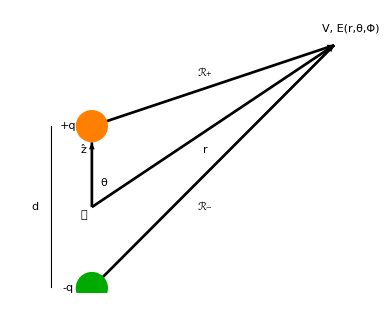

```mathematica
Graphics[{Style[Text["𝒪",{-.1,-.1}],12],Thickness[0.005],Arrow[{{0,0},{3,2}}],Style[Text["r",{1.4,.7}],18,Bold], Style[Text["ℛ_+",{1.4,1.65}],18,Bold],Style[Text["ℛ_-",{1.4,0}],18,Bold],Style[Text["+q",{-.3,1}],16],  Style[Text["-q",{-.3,-1}],16], Style[Text["θ",{.15,.3}],12],Style[Text[OverHat["z"],{-.1,.7}],12],Style[Text["V, E(r,θ,Φ)",{3.2,2.2}],12],Style[Text["d",{-.7,0}],12],Arrow[{{0,0},{0,.8}}],Arrow[{{0,1},{3,2}}],Arrow[{{0,-1},{3,2}}],{Thickness[0.002],Line[{{-.5,-1},{-.5,1}}]},{Orange,PointSize[.06],Point[{0,1} ],Darker[Green],Point[{0,-1} ]},}]
```

ℛ_+=r^2+(d/2)^2-r d cosθ

ℛ_-=r^2+(d/2)^2+r d cosθ

1/(ℛ_+)≃1/r 1/(√(1-(d/r) cosθ))≃1/r(1+d/(2r)cosθ)

1/(ℛ_-)≃1/r 1/(√(1-(d/r) cosθ))≃1/r(1-d/(2r)cosθ)

Define

p≡q d ẑ=

V=q/(4π ("ε")_0)[1/(ℛ_+)-1/(ℛ_-)]=(q d cosθ)/(4π ("ε")_0 r^2)=(p \[Application] r̂)/(4π ("ε")_0 r^2)

The electric field is the negative gradient of V.

Calculate the potential for a dipole with charges ±q at locations ±𝓏.

```mathematica
ClearAll["Global`*"];pos={0,0,d/2}; neg={0,0,-d/2}; r={x,y,z}; 𝓅=r-pos; 𝓂=r-neg;V=q/(4π Subscript[ε, 0])(1/(√(𝓅.𝓅))-1/(√(𝓂.𝓂)))
```

(q (1/(√(x^2+y^2+(-d/2+z)^2))-1/(√(x^2+y^2+(d/2+z)^2))))/(4 π ε_0)

The demonstration at the opening of this chapter illustrates the dipole potential.

Calculate the electric field of the dipole.

```mathematica
Ε=-Grad[V,{x,y,z}]
```

{-(q (-x/((x^2+y^2+(-d/2+z)^2)^(3/2))+x/((x^2+y^2+(d/2+z)^2)^(3/2))))/(4 π ε_0),-(q (-y/((x^2+y^2+(-d/2+z)^2)^(3/2))+y/((x^2+y^2+(d/2+z)^2)^(3/2))))/(4 π ε_0),-(q (-(-d/2+z)/((x^2+y^2+(-d/2+z)^2)^(3/2))+(d/2+z)/((x^2+y^2+(d/2+z)^2)^(3/2))))/(4 π ε_0)}

Draw the electric field lines for a physical dipole.

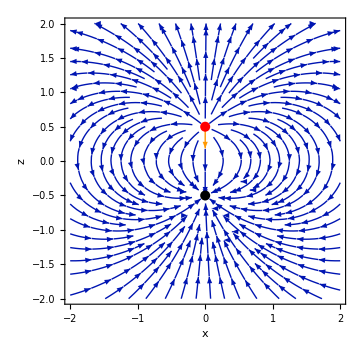

```mathematica
StreamPlot[Ε[[{1,3}]]/.{y->0,d->1,q->1,Subscript[ε, 0]->1},{x,-2,2},{z,-2,2},]
```

Draw the dipole field lines in 3D.

```mathematica
Show[StreamPlot3D[{x,y,z-1/2}/Norm[{x,y,z-1/2}]^3-{x,y,z+1/2}/Norm[{x,y,z+1/2}]^3,{x,-2,2},{y,-2,2},{z,-2,2},],Graphics3D[{Red,Sphere[{0,0,1/2},0.15],Black,Sphere[{0,0,-1/2},0.15]}]]
```

-Graphics3D-

Wolfram Research (2021), StreamPlot3D, Wolfram Language function, https://reference.wolfram.com/language/ref/StreamPlot3D.html.

Transform the potential to spherical coordinates.

```mathematica
Clear[r]; VT=TransformedField[ "Cartesian"-> "Spherical" , 
  V, {x, y, z}  ->{r, θ, ϕ}]//Simplify
```

(q (1/(√(d^2+4 r^2-4 d r Cos[θ]))-1/(√(d^2+4 r^2+4 d r Cos[θ]))))/(2 π ε_0)

At a long distance away compared to its size (r >> d), the dipole potential looks simple.

Expand the dipole potential, valid for large r.

```mathematica
Simplify[Series[VT,r->∞],{r>0}]
```

(d q Cos[θ])/(4 π ε_0 r^2)+O[1/r]^3

Since p = q d,

V=(p cosθ)/(4π ("ε")_0 r^2)

This is the potential for an ideal dipole. It is the dipole approximation of the physical dipole. It is equivalent to taking the limit d→0 while keeping p = q d constant. It is a dipole that one can never get close to because it is infinitely small.

Calculate the electric field of an ideal dipole.

```mathematica
V=(p Cos[θ])/(4 π Subscript[ε, 0] r^2);Ε=-Grad[V, {r, θ, φ}, "Spherical"]
```

{(p Cos[θ])/(2 π r^3 ε_0),(p Sin[θ])/(4 π r^3 ε_0),0}

Transform the electric field to Cartesian coordinates.

```mathematica
ET=TransformedField["Spherical" -> "Cartesian", 
  Ε, {r, θ, φ} -> {x, y, z}]//FullSimplify
```

{(3 p x z)/(4 π (x^2+y^2+z^2)^(5/2) ε_0),(3 p y z)/(4 π (x^2+y^2+z^2)^(5/2) ε_0),-(p (x^2+y^2-2 z^2))/(4 π (x^2+y^2+z^2)^(5/2) ε_0)}

Verify that the coordinate transformation produces the same result as taking the gradient in Cartesian.

```mathematica
VT=TransformedField[ "Spherical" -> "Cartesian", 
  V, {r, θ, φ} -> {x, y, z}];ET == -Grad[VT, {x, y, z}] // Simplify
```

True

Verify that the curl is zero.

```mathematica
Curl[Ε,{x,y,z}]
```

{0,0,0}

Draw the electric field lines for the ideal dipole.

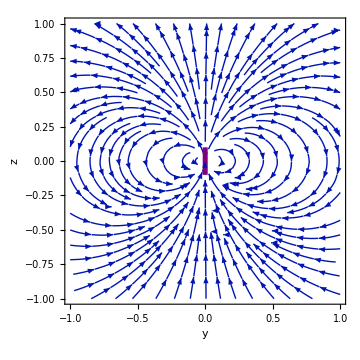

```mathematica
With[{ETP = 4 π Subscript[ε, 0] ET},  StreamPlot[Rest[ETP /. {p -> 1, x -> 0}] , {y, -1, 1}, {z, -1, 1}, ]]
```

Draw the electric field lines for an ideal dipole in 3D.

```mathematica
With[{ETP = 4 π Subscript[ε, 0] ET},Show[StreamPlot3D[ETP/.p->1,{x,-2,2},{y,-2,2},{z,-2,2},],Graphics3D[{Thickness[0.01],Purple,Arrowheads[0.03],Arrow[{{0,0,-.25},{0,0,.15}}]}]]]
```

-Graphics3D-

1.9 Energy of a Charge Distribution

The work done in moving a charge from a to b in an electric field is

W=∫_a^b F\[Application]ⅆ𝕝=-Q∫_a^b E\[Application]ⅆ𝕝=Q [V(b)-V(a)]

To bring a charge in from infinity to position r requires work

W=Q V(r)

Let’s go though the steps in bringing three charges together. In each case, the field for the nth charge is due to the other n-1 charges. The first charge comes in for free since no electric field exists yet. The second charge requires work

W_2=(q_1 q_2)/(4π ("ε")_0 R_12)

The third charge requires work

W_3=q_3/(4π ("ε")_0)(q_1/R_13+q_2/R_23)

The total work is

W_2+W_3=1/(4π ("ε")_0)((q_1 q_2)/R_12+(q_1 q_3)/R_13+(q_2 q_3)/R_23)

Draw a configuration of 3 charges.

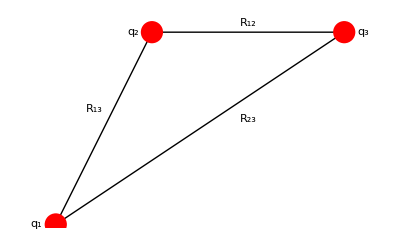

```mathematica
Graphics[{Line[{{{0,0},{1,2}},{{1,2},{3,2}},{{3,2},{0,0}}}],PointSize[.04],Red,Point[{{0,0},{1,2},{3,2}}],Black,Text[Subscript[R, 12],{2,2.1}],Text[Subscript[R, 23],{2,1.1}],Text[Subscript[R, 13],{.4,1.2}],Text[Subscript[q, 1],{-.2,0}],Text[Subscript[q, 2],{0.8,2}],Text[Subscript[q, 3],{3.2,2}]}]
```

Calculate the work to assemble 3 same-sign elementary charges in positions {0,0,0} nm, {1,2,0} nm, and {3,2,0} nm.

```mathematica
R={{0,0}Quantity[, "Nanometers"],{1,2}Quantity[, "Nanometers"],{2,3}Quantity[, "Nanometers"]} ; Subscript[R, 12]=Norm[R[[1]]-R[[2]]];  Subscript[R, 13]=Norm[R[[1]]-R[[3]]];  Subscript[R, 23]=Norm[R[[2]]-R[[3]]]; N[UnitConvert[Quantity[, "ElementaryCharge"]^2/(4π Quantity[, "ElectricConstant"])(1/Subscript[R, 12]+1/Subscript[R, 13]+1/Subscript[R, 23]), Quantity[, "Electronvolts"]],2]
```

2.1 eV

The general formula for the work required to assemble n charges is

W=1/(4π ("ε")_0)∑ _(i=1)^n  ∑_(j >1)^n (q_i q_j)/R_ij=1/2 1/(4π ("ε")_0)∑ _(i=1)^n  ∑_(j ≠i)^n (q_i q_j)/R_ij=1/2∑ _(i=1)^n q_i V(r_i)

For a continuous charge distribution,

W=1/2∫ρ Vⅆ𝕍'=(("ε")_0)/2∫ (∇\[Application]E)Vⅆ𝕍'

Integrating by parts

The first term on the right is zero because we may use the divergence theorem and choose the surrounding surface to be at infinity where both E and V vanish.

∫ ∇\[Application](E V)ⅆ𝕍'=∫ (EV)\[Application]ⅆ𝕒'=0

This means that the volume integral must go over all space and we get (substituting the field for negative gradient of V)

W=(("ε")_0)/2∫ E^2 ⅆ𝕍'

This is a handy form of the stored energy and we are going to get a similar result for the magnetic field. The stored energy per volume goes as the square of the field.

We end up with 2 ways to calculate the stored energy,

W=1/2∫ρ Vⅆ𝕍'    only integrate over the volume which the charge occupies

or

W=(("ε")_0)/2∫ E^2 ⅆ𝕍'   integrate over all space

There seems to be a subtle inconsistency here. The formula for discrete charges can have positive or negative contributions while the formula for continuous charges is manifestly positive. This is because the continuous formula includes the energy to assemble the charges themselves. Thus, we must be careful to specify what we mean when talking about the energy of a charge distribution.

The classical electron radius is where the electric potential energy equals the mass energy.

Calculate the classical electron radius of the electron.

```mathematica
ClearAll["Global`*"];N[UnitConvert[SolveValues[Quantity[, "ElementaryCharge"]^2/(4π Quantity[, "ElectricConstant"]r)== Entity["Particle","Electron"][EntityProperty["Particle","Mass"]] Quantity[, "SpeedOfLight"]^2,r][[1]],Quantity[, "Femtometers"]],2]//Quiet
```

2.8 fm

There is nothing special about this number. Experiments have been performed on the electron at orders of magnitude smaller distance scales. Everything so far shows that the electron has no structure down to a scale of 10^-19 m, yet has a physical size given by its quantum wave properties.

1.10  Conductors

Conductors are materials in which one or more electrons per atom are free to move. They move rapidly if you try to introduce an electric field. Electrons are pushed and they move essentially instantly until they are no longer pushed. This results in a remarkable number of properties:

■    E = 0 within the conducting material.

Otherwise the charges would experience a net force inside the material, and be pushed until that isn’t true.

■    ρ = 0 within the conducting material.

Otherwise the electric field wouldn’t be 0.

■   All excess charge must reside on the conducting surface.

Due to ρ = 0 inside.

■   The conductor is at equipotential.

The whole object has a constant potential, so that E = - ∇V = 0.

■   The electric field just outside the conductor is perpendicular to the surface.

Since V is constant inside, and ∇V points in the direction of changing V — which has to be perpendicular to the surface.

The electric field near a flat conductor with charge density σ may be found using Gauss’s law. Take the Gaussian surface (cylinder of radius d) to extend into the conductor and terminate inside. The field is non-zero only on the circular face outside.

∮  E· ⅆ𝕒= E ( π d^2 )=q_in/(("ε")_0)=(σ π d^2)/(("ε")_0)

Solving for E:

E =σ/(("ε")_0)

Show the Gaussian cylinder (green) both inside and outside the conductor (orange).

```mathematica
Graphics3D[{Opacity[0.3],Orange,Cuboid[{0,-20,-20},{4,20,20}], Green, Cylinder[{{2,0,0},{6,0,0}},2],Opacity[1],Black, Thickness[0.007],Arrow[{{6,0,0},{12,0,0}}],Text["E",{13,0, 0}]},Boxed->False]
```

-Graphics3D-

1.11 Laplace’s Equation

We have seen that

∇\[Application]E = ρ/(("ε")_0)   and     E =-∇ V

which can be combined to give Poisson’s equation.

∇\[Application]E =∇\[Application](- ∇V)=-∇^2 V= ρ/(("ε")_0)

For the special case where there is no charge is some region, we get Laplace’s equation:

∇^2 V= 0

1.11.1 Average Potential Over a Spherical Surface

Consider a point charge q. The potential averaged over a sphere at a distance r has a simple value. It is equal to the value at the center.

Calculate the average potential on a sphere a distance r away from a point charge q.

```mathematica
ClearAll["Global`*"]; $Assumptions={r>R, r>0, R>0};ℛ={0,0,r}-FromSphericalCoordinates[{R,ϑ,0}]; 1/(4π R^2)q/(4π Subscript[ε, 0])2π∫_0^π (R^2 Sin[ϑ])/(√(ℛ.ℛ))ⅆϑ
```

q/(4 π r ε_0)

By superposition, this is true for any number of charges. There is an important conclusion to be drawn from this. The potential can have no local maxima or minima. The maxima or minima must occur on the boundaries. This leads to a uniqueness theorem: Specifying the potential on the boundary surface uniquely determines the potential inside. To see that this is true suppose that there were 2 solutions  V_1 and V_2. Take the difference, V_2 - V_1. The difference itself is a solution of Laplace’s equation, but a solution which is zero on the boundary. If it is zero on the boundary, then it must be zero everywhere because there can be no extrema except on the boundary. Therefore, V_1= V_2 and there is only one solution.

1.11.2 Solutions of Laplace’s Equation

Consider a hollow rectangular pipe (a x b) with the sides x = 0 and x = a held at constant potential V_0 while the other 2 sides, y = 0 and y = b, are at zero potential. This is effectively a 2D problem.

Draw the boundary conditions for the solution of Laplace’s Equation.

```mathematica
Graphics3D[{Opacity[0.3],Orange,Cuboid[{0,0,0},{4,0,20}],Cuboid[{0,2,0},{4,2,20}],Green,Cuboid[{0,0,0},{0,2,20}],Cuboid[{4,0,0},{4,2,20}],Black, Opacity[1],Style[Text["V_0",{-.2,1, 0}],16],Style[Text["V=0",{2,-.2, 0}],16],Style[Text["b",{4.2,2, 0}],16],Style[Text["0",{4.2,0, 0}],16],Style[Text["a",{0,-.2, 0}],16],Style[Text["V=0",{1.8,2.2, 0}],16],Style[Text["V_0",{4.4,1, 0}],16]},Boxed->False]
```

-Graphics3D-

Separation of variables with the given boundary conditions leads to a solution of the form

V(x,y)= ∑ _(n=1)^∞ C_n cosh(nπx/b)sin(nπy/b)

where n is a positive integer. The boundary condition on x gives

V(a,y)=V_0= ∑ _(n=1)^∞ C_n cosh(nπa/b)sin(nπ y/b)

This is solved by Fourier analysis which involves multiplying each side by sin(n’π y/b) by and integrating over y from 0 to b to get the constants C_n.

The solution may be obtained analytically by defining a set of 5 equations, one of which is Laplace’s equation, the other 4 being the boundary conditions on the sides.

Solve Laplace’s equation.

```mathematica
ClearAll["Global`*"];eqns={Laplacian[u[x,y],{x,y}]==0,u[0,y]==V, u[a,y]==V,u[x,0]==0, u[x,b]==0};
sol=FullSimplify[DSolveValue[eqns,u[x,y],{x,y}]]
```

(4 V Csch[(a π K[1])/b] Sign[b] Sin[(π y K[1])/b] Sin[(π K[1])/(2 Sign[b])]^2 (Sinh[(π (a-x) K[1])/b]+Sinh[(π x K[1])/b]))/(π K[1])K[1]1∞

Plot the solution for a = 2 and b = 1, keeping 500 terms.

```mathematica
a=2;b=1;V=1;Ω=Rectangle[{0,0},{a,b}];
solution=sol/.{∞->500}//Activate;
Plot3D[solution//Evaluate,{x,y}∈Ω,]
```

-Graphics3D-

Now remove the boundary at x = a such that the region is now open on one end.

Draw the surface.

```mathematica
Graphics3D[{Opacity[0.3],Orange,Cuboid[{0,0,0},{4,0,20}],Cuboid[{0,2,0},{4,2,20}],Green,Cuboid[{0,0,0},{0,2,20}],Black, Opacity[1],Style[Text["V_0",{-.2,1, 0}],16],Style[Text["V=0",{2,-.2, 0}],16],Style[Text["V=0",{1.8,2.2, 0}],16],Style[Text["b",-{.2,0, 0}],16],Style[Text["0",{-.2, 2,0}],16],},Boxed->False]
```

-Graphics3D-

Solve Laplace’s equation with an open boundary.

```mathematica
ClearAll["Global`*"];eqns={Laplacian[u[x,y],{x,y}]==0,u[0,y]==V, u[x,0]==0, u[x,b]==0};
sol=FullSimplify[DSolveValue[eqns,u[x,y],{x,y}]]/.{b->2,V->1};Plot3D[sol,{x,0,3},{y,0,1},]
```

-Graphics3D-

This is a new feature of Mathematica 12.3 as reported by Stephen Wolfram (2021), https://blog.wolfram.com/2021/05/20/launching-version-12-3-of-wolfram-language-mathematica/

Separation in spherical coordinates follows the same technique. The solution of the separated radial equation in spherical coordinates,

1/R ⅆ/ⅆr(r^2 ⅆR/ⅆr)=constant

is

R(r)=A r^l+B/r^(l+1)

The separation constant is

```mathematica
Clear[l]; R=A r^l+B/r^(l+1);FullSimplify[D[(r^2 D[R, r]), r]/R]
```

l (1+l)

The solutions to the theta part of the separated radial equation in spherical coordinates

1/(Θ sinθ)ⅆ/ⅆθ(sinθ ⅆΘ/ⅆθ)=constant

are Legendre polynomials.

The result is that if there is no phi dependence, the potential may be written

V(r,θ)=∑_(l=0)^∞ (A_l r^l+B_l/r^(l+1))P_l(cosθ)

The key step in the solution is to use

∫_-1^1 P_n(x) P_m(x)ⅆx=2/(2n +1)δ_nm

The following demonstration solves Laplace’s equation for arbitrary boundary conditions on various geometries. A certain sinusoidal boundary condition produces a solution in the shape of a “Pringle” chip.

```mathematica
ClearAll["Global`*"];Manipulate[Module[{sol},Check[sol=NDSolve[{Laplacian[f[x,y],{x,y}]==0,DirichletCondition[f[x,y]==ToExpression[bounds,TraditionalForm],True]},f,{x,y}∈Region];Column[{Plot3D[First[f/.sol][x,y],{x,y}∈Region,],Plot[ToExpression[bounds,TraditionalForm]/.{x->Cos[ϕ],y->Sin[ϕ]},{ϕ,0,2π},]}],"Something went wrong, try capitalizing function names"]],{{bounds,"sin(x y)","Enter a Function of x and y:"},InputField[#,String]&},{Region,{Disk[]->"Disk",Annulus[]->"Annulus",RegularPolygon[3]->"Triangle",Rectangle[-1/2 {1,1}]->"Square",RegularPolygon[8]->"Octagon"}}]
```

1.12 Summary of E, V, and ρ

Here is a summary of how to calculate one quantity from another in electrostatics. Keep in mind that the concept of writing the field in terms of the gradient of a scalar potential exists only in the case of statics, where the curl of the electric field is zero. This needs modification in order to accommodate time-varying fields.

ρ→ E             E=1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r'))/ℛ^2 ℛ̂
		E->ρ              ρ= ("ε")_0∇\[Application]E
		E→V              ΔV=∫ E\[Application]ⅆ𝕝       V(r)=-∫_∞^r E\[Application]ⅆr'
		V→E             E =-∇ V
		ρ→ V            V=1/(4π  ("ε")_0)∫ ⅆ𝕍'(ρ(r'))/ℛ 
		V->ρ             ρ=- ("ε")_0∇^2 V

Exercises

Place 17 elementary charges at equal spacing around the circumference of a circle.
a) Calculate the electric field at the center of the circle.
b) Remove one charge and show by direct calculation that you get the same answer as expected from using the superposition principle.

a) Calculate the the electric force on a charge at  "e" at {1,0,0} nm  from 100 other elementary charges with random signs ± "e" at random positions {x,y,z} in the range 0 to 1 nm.
b) Do this 10 times and make a histograms of the field components..

Find the electric potential at the center of a gold nucleus with radius 6 fm and charge equal to 79  "e" distributed uniformly in the spherical volume. Give a numerical answer in V.

A long cylinder of radius R has charge has density given by λ = a r^2 for r < R.
a)  Calculate the electric field both inside and outside the cylinder. 
b) Plot the result.
c) Give a numerical value of E in V/m at r = 1 m for R =  1 mm, and a =  3 μC/m^3.

Consider two long concentric cylinders of radii a and b and surface charge densities σ_a and σ_b, respectively. Calculate the electric field everywhere.

Take point A to be at a radial distance R from a hemisphere of uniform surface charge density σ. Take point B to be on the hemisphere (along  it symmetry axis. Calculate the potential difference between points A and B.

Calculate the electric field due to a sphere of charge Q of radius R whose density varied as βr^2where β = 5Q/4πR^5.
a) Calculate the potential everywhere inside the sphere. 
b) Use this result for V to calculate the electrostatic energy of the sphere (energy required to assemble it).
c) Check your answer by integrating E^2 over all space.

Consider a frustum (piece of a cone with its top cut off parallel to its base) with uniform charge density ρ throughout its volume. The height of the frustum is d and the radius of its base is a.
a) Find the electric field at point P, where the tip of a full cone would be.
b) Now consider a whole cone of charge. What happens to the electric field at point P and why?

The leading term for the physical dipole is the ideal dipole. Calculate the next 2 terms.

Consider a dipole made of two uniform rings of charge ±λ of radius R and distance d apart. Calculate the potential at a distance r to order 1/r^3.

A spherical shell of radius a and surface charge density σ is sandwiched between two infinite planes with surface charge densities σ and −σ. Take the electric potential at positive infinity  to be zero.
a) Calculate the electric potential at the center of the shell.
b) What is the potential at −∞ ?

Consider an electric potential of the form V =Ce^-ikr where C and k are constant. 
a) Find the electric field corresponding to this potential.
c) Find the charge distribution.
d) Find the total charge.

A sphere has a surface charge density σ = B sin^2θ where θ is the usual polar angle. Find the electric field everywhere.

Earnshaw’s theorem states that you can’t have stable equilibrium with electrostatic forces alone. Consider the case of 8 identical charges (q) held fixed at the corners of a cube. Show that a charge placed at the center is not in stable equilibrium.

A spherical shell of radius R has a charge distribution σ = q sin(2θ) / R^2where θ is the usual polar angle. Calculate the electric dipole moment.

A cube has 3 neighboring sides at voltages V_0, 2V_0, and 3V_0 and the other 3 sides at 0 V. Find the potential inside the cube.